```mathematica
f[t_,y_]:=t^3*Cos[y/(√5)]
```

```mathematica
t0=0;tm=1;y0=3;
```

```mathematica
eps=0.0015;m=10
```

10

h= 1/10 m= 10

U= {{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1},{3,3.00001,3.00009,3.00046,3.00145,3.00354,3.00731,3.01346,3.02275,3.03596,3.0538}}

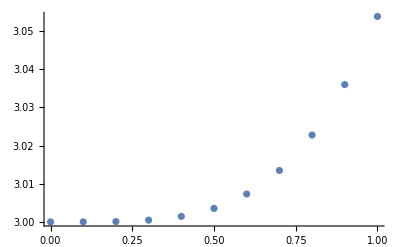

h= 1/9 m= 9

U= {{0,1/9,2/9,1/3,4/9,5/9,2/3,7/9,8/9,1},{3,3.00001,3.00014,3.0007,3.00221,3.00538,3.0111,3.02037,3.03427,3.0538}}

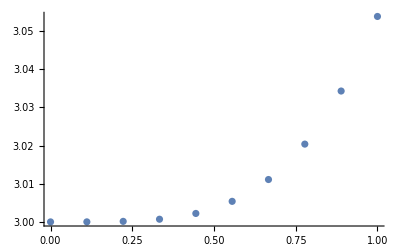

max: t=1 d= 6.12665×10^-9

epsl= 4.08444×10^-10

h= 1/8 m= 8

U= {{0,1/8,1/4,3/8,1/2,5/8,3/4,7/8,1},{3,3.00001,3.00022,3.00112,3.00354,3.00859,3.01766,3.03225,3.0538}}

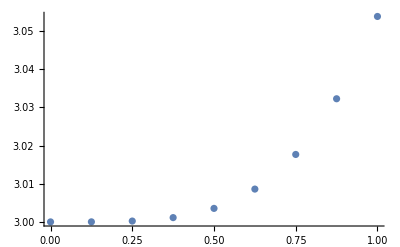

max: t=1 d= 1.22264×10^-8

epsl= 8.15093×10^-10

h= 1/7 m= 7

U= {{0,1/7,2/7,3/7,4/7,5/7,6/7,1},{3,3.00002,3.00038,3.00191,3.00602,3.01457,3.02977,3.0538}}

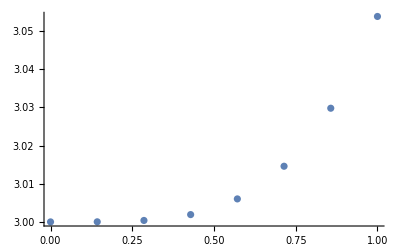

max: t=1 d= 2.6546×10^-8

epsl= 1.76973×10^-9

h= 1/6 m= 6

U= {{0,1/6,1/3,1/2,2/3,5/6,1},{3,3.00004,3.0007,3.00354,3.0111,3.02668,3.0538}}

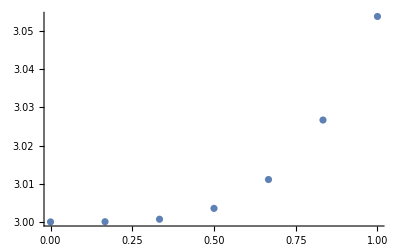

max: t=1 d= 6.42748×10^-8

epsl= 4.28499×10^-9

h= 1/5 m= 5

U= {{0,1/5,2/5,3/5,4/5,1},{3,3.00009,3.00145,3.00731,3.02275,3.0538}}

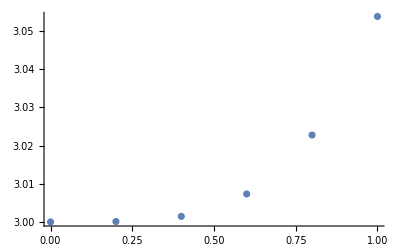

max: t=1 d= 1.80158×10^-7

epsl= 1.20105×10^-8

h= 1/4 m= 4

U= {{0,1/4,1/2,3/4,1},{3,3.00022,3.00354,3.01766,3.0538}}

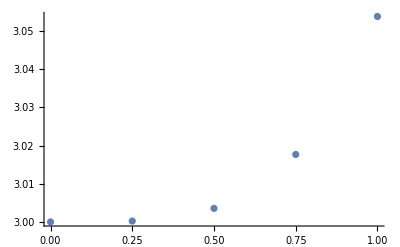

max: t=1 d= 6.21206×10^-7

epsl= 4.14137×10^-8

h= 1/3 m= 3

U= {{0,1/3,2/3,1},{3,3.0007,3.0111,3.0538}}

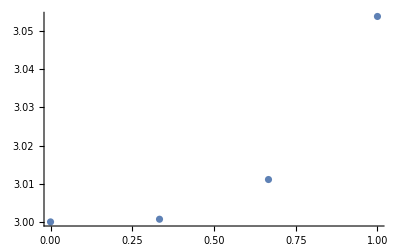

max: t=1 d= 2.94083×10^-6

epsl= 1.96055×10^-7

h= 1/2 m= 2

U= {{0,1/2,1},{3,3.00354,3.05383}}

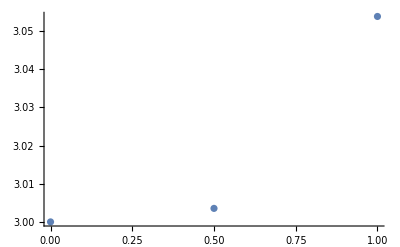

max: t=1 d= 0.00002423

epsl= 1.61534×10^-6

h= 1 m= 1

U= {{0,1},{3,3.05452}}

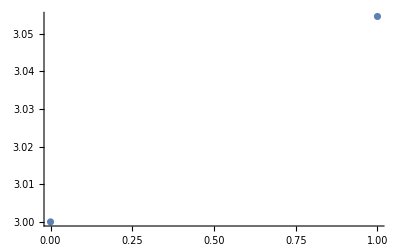

max: t=1 d= 0.000694047

epsl= 0.0000462698

```mathematica
func1[f_,t0_,tm_,y0_,m_,eps_]:=Block[{k1,k2,k3,k4,h,U,t,y,epsl,cm,A,u,B,cd,max,ct},
k1[h_]:=f[t,y];
k2[h_]:=f[t+0.5*h,y+0.5*h*k1 [h]];
k3[h_]:=f[t+0.5*h, y+0.5*h*k2[h]];
k4[h_]:=f [t+h, y+h*k3[h]];
epsl=0;
cm=m;
h=(tm-t0)/cm;
Print["h= ",h," m= ",cm];
U = Table[0,{i,2},{j,cm+1}];
U[[1,1]]=t0;U[[2,1]]=y0;
t=t0;y=y0;
Do[dy=h*(k1[h]+2*k2[h]+2*k3[h]+k4[h])/6;
t=t+h;
y=y+dy;
U[[1,i+1]]=t;
U[[2,i+1]]=y,{i,1,cm}];
Print["U= ",U];
Print[ListPlot[Transpose[{U[[1]],U[[2]]}]]];
cm=cm-1;
B = Table[U[[i,j]],{i,2},{j,m+1}];
A={};
A=Append[A,U];
While[cm>0,
h=(tm-t0)/cm;
Print["h= ",h, " m= ",cm];
U = Table[0,{i,2},{j,cm+1}];
U[[1,1]]=t0;U[[2,1]]=y0;
t=t0;y=y0;
Do[dy=h*(k1[h]+2*k2[h]+2*k3[h]+k4[h])/6;
t=t+h;
y=y+dy;
U[[1,i+1]]=t;
U[[2,i+1]]=y,{i,1,cm}];
Print["U= ",U];
Print[ListPlot[Transpose[{U[[1]],U[[2]]}]]];
A=Append[A,U];
max = 0;
cd = 0;
ct=t0;
Do[Do[If[B[[1,j]]==U[[1,i]],Block[{},cd=Abs[U[[2,i]]-B[[2,j]]];Break],cd]
,{j,2,cm+2}];If[cd>max,Block[{},max=cd;ct=U[[1,i]]],max]
,{i,2,cm+1}];
If[max>0,Block[{},Print["max: t=",ct," d= ",max];
epsl=max/(2^4-1);
Print["epsl= ",epsl];
If[epsl>eps,Break,epsl]],""];
B = Table[U[[i,j]],{i,2},{j,cm+1}];
cm=cm-1;
];
A
];
AU=func1[f,t0,tm,y0,m,eps];
```

```mathematica
mh=1/3;ym=AU[[8,2,4]];
```

h= 1/3 m= 3

U= {{0,1/3,2/3,1},{3.00001,3.00071,3.01111,3.0538}}

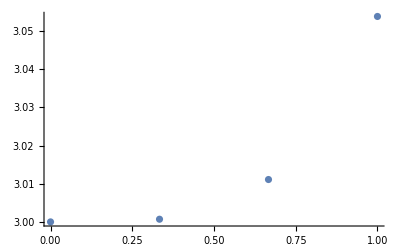

{{0,1/3,2/3,1},{3.00001,3.00071,3.01111,3.0538}}

```mathematica
func2[f_,t0_,tm_,ym_,mh_]:=Block[{k1,k2,k3,k4,U,t,y,m},
k1[h_]:=f[t,y];
k2[h_]:=f[t-0.5*h,y-0.5*h*k1 [h]];
k3[h_]:=f[t-0.5*h, y-0.5*h*k2[h]];
k4[h_]:=f [t-h, y-h*k3[h]];
m=(tm-t0)/mh;
Print["h= ",mh," m= ",m];
U = Table[0,{i,2},{j,m+1}];
U[[1,m+1]]=tm;U[[2,m+1]]=ym;
t=tm;y=ym;
Do[dy=mh*(k1[mh]+2*k2[mh]+2*k3[mh]+k4[mh])/6;
t=t-mh;
y=y-dy;
U[[1,m+1-i]]=t;
U[[2,m+1-i]]=y,{i,1,m}];
Print["U= ",U];
Print[ListPlot[Transpose[{U[[1]],U[[2]]}]]];
U
];
AU2=func2[f,t0,tm,ym,mh]
```

```mathematica
func3[f_,t0_,tm_,y0_,mh_]:=Block[{U,t,y,k1,k2,k3,k4,k5,k6,epsl,m},
k1[h_]:=f[t,y];
k2[h_]:=f[t+0.25*h,y+0.25*h*k1 [h]];
k3[h_]:=f[t+3/8*h, y+3/32*h*k1[h]+9/32*h*k2[h]];
k4[h_]:=f [t+12/13*h, y+h*(1932/2197*k1[h]-7200/2197*k2[h]+7296/2197*k3[h])];
k5[h_]:=f[t+h,y+h*(439/216*k1[h]-8*k2[h]+3680/513*k3[h]-845/4104*k4[h])];
k6[h_]:=f[t+0.5*h,y-h*(8/27*k1[h]+2*k2[h]-3544/2565*k3[h]+1859/4104*k4[h]-11/40*k5[h])];
m=(tm-t0)/mh;
Print["h= ",mh," m= ",m];
U = Table[0,{i,3},{j,m+1}];
U[[1,1]]=t0;U[[2,1]]=y0;U[[3,1]]=0;
t=t0;y=y0;
Do[dy=mh*(25/216*k1[mh]+1408/2565*k3[mh]+2197/4104*k4[mh]-1/5*k5[mh]);
t=t+mh;
y=y+dy;
U[[1,i+1]]=t;
U[[2,i+1]]=y;
epsl=mh*(k1[mh]/360-128/4275*k3[mh]-2197/75240*k4[mh]+k5[mh]/50+2/55*k6[mh]);
U[[3,i+1]]=epsl,{i,1,m}];
Print["U= ",U];
Print[ListPlot[Transpose[{U[[1]],U[[2]]}]]];
U
];
AU3=func3[f,t0,tm,y0,mh];
```

h= 1/3 m= 3

U= {{0,1/3,2/3,1},{3,3.0007,3.0111,3.0538},{0,4.81874×10^-6,0.000135038,0.00104376}}

-Graphics-

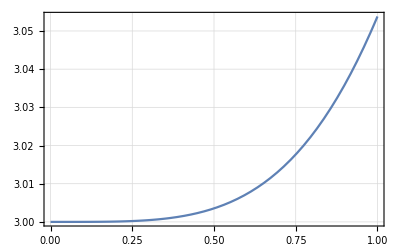

{3.}

{3.0007}

{3.0111}

{3.0538}

{0,1/3,2/3,1}

```mathematica
wolfexpl[f_,t0_,tm_,y0_]:=Block[{Y,y},
Y=NDSolve[{y'[t] == f, y[0] == y0}, y, {t, t0, tm}, Method->"ExplicitRungeKutta"];
y[t_]=y[t]/.Y;
Print[Plot[y[t], {t,t0,tm},Frame->True,GridLines->Automatic ]];
Print[y[0]];
Print[y[1/3]];
Print[y[2/3]];
Print[y[1]];
y
];
wolfexpl[t^3*Cos[y[t]/(√5)],t0,tm,y0];
{0,1/3,2/3,1}
```

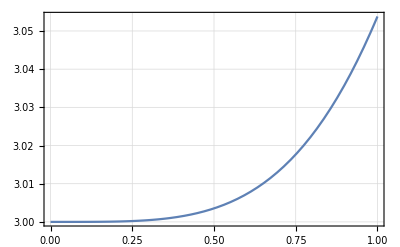

{3.}

{3.0007}

{3.0111}

{3.0538}

```mathematica
wolfexpl[f_,t0_,tm_,y0_]:=Block[{Y,y},
Y=NDSolve[{y'[t] == f, y[0] == y0}, y, {t, t0, tm}, Method->"ImplicitRungeKutta"];
y[t_]=y[t]/.Y;
Print[Plot[y[t], {t,t0,tm},Frame->True,GridLines->Automatic ]];
Print[y[0]];
Print[y[1/3]];
Print[y[2/3]];
Print[y[1]];
y
];
wolfexpl[t^3*Cos[y[t]/(√5)],t0,tm,y0];
```